# Kicks

The Kicks package provides optimised functions for computing the linear momentum radiated in gravitational waves from the spherical harmonic modes of Ψ_4.  There is an example dataset used by this documentation from a binary black hole simulation with mass ratio 1:3, both BHs having dimensionless spin 0.8 initially oriented in the orbital plane.  This package uses the ReadPsi4 function defined in the NR package, so it supports all the mode decomposition thorns supported by that package.  This includes Multipole (HDF5 and ASCII) and Ylm_Decomp.

```mathematica
<<nrmma`
```

## Full API

The full list of Kicks functions is below.  Click on one of them for documentation:

```mathematica
?Kicks`*
```

## Examples

```mathematica
run="~/Simulations/spinkicks/q3s08_4e";
```

Here we take the radius r = 100, the z-component, and use only the modes up to l = 4.

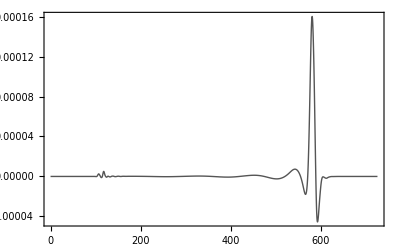

```mathematica
PresentationListLinePlot[LinearMomentumFlux[run, 3, 100, 4],PlotRange->All]
```

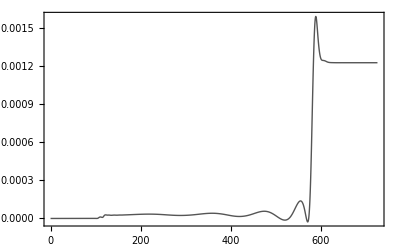

```mathematica
PresentationListLinePlot[LinearMomentumRadiated[run, 3, 100, 4],PlotRange->All]
```

The kicks are measured in km/s.

```mathematica
Kick[run, 3, 100, 4]
```

367.451

```mathematica
KickVector[run,100,2]
```

{-242.141,-224.672,293.946}

Extrapolate the z-component of the kick to r = ∞:

```mathematica
rads=ReadPsi4Radii[run]
```

{30,40,46,54,65,81,100}

```mathematica
vzOfr=Monitor[Table[{r,Kick[run,3,r,4]},{r,rads}],r]
```

{{30,389.865},{40,381.26},{46,377.696},{54,376.584},{65,371.904},{81,369.368},{100,367.451}}

We extrapolate by fitting to a first degree polynomial in 1/r:

	v(r) = v_∞ + v_1/r

```mathematica
extrap=ExtrapolateScalarFull[1,vzOfr]
```

{ExtrapolatedValue→357.658,Data→{{0.0333333,389.865},{0.025,381.26},{0.0217391,377.696},{0.0185185,376.584},{0.0153846,371.904},{0.0123457,369.368},{0.01,367.451}},ExtrapolatedCurve→{{0.,357.658},{0.00333333,360.85},{0.00666667,364.041},{0.01,367.233},{0.0133333,370.424},{0.0166667,373.616},{0.02,376.807},{0.0233333,379.999},{0.0266667,383.19},{0.03,386.381},{0.0333333,389.573}}}

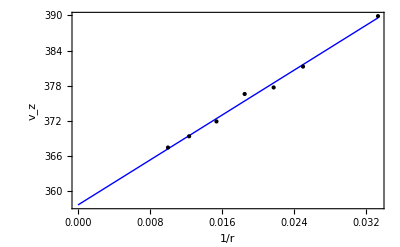

```mathematica
PresentationListLinePlot[{Data/.extrap,ExtrapolatedCurve/.extrap},Joined->{False,True},FrameLabel->{"1/r","v_z"},PlotRange->{0,All}]
```

The extrapolated kick is

```mathematica
ExtrapolatedValue/.extrap
```

357.658

### Extrapolate the flux

We take only the highest 4 radii, because the lower radii don’t extrapolate well (probably too low).  Again we look at the z component of the flux up to l = 4.

```mathematica
pDotOfr=Monitor[Table[{r,LinearMomentumFlux[run, 3, r, 4]},{r,Take[rads,-4]}],r]
```

{{54,DataTable[...]},{65,DataTable[...]},{81,DataTable[...]},{100,DataTable[...]}}

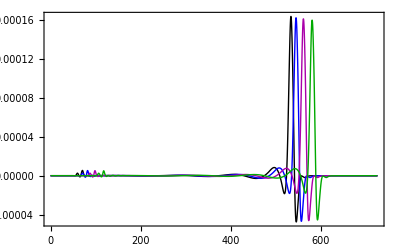

```mathematica
PresentationListLinePlot[Map[Last,pDotOfr],PlotRange->All]
```

```mathematica
mADM=ReadADMMass[run]
```

0.991196

```mathematica
pDot=ExtrapolateRadiatedQuantity[pDotOfr,MassADM->mADM]
```

DataTable[...]

```mathematica
shiftedpDots=MapThread[ShiftDataTable[-TortoiseCoordinate[#1,mADM],#2]&,Transpose@pDotOfr]
```

{DataTable[...],DataTable[...],DataTable[...],DataTable[...]}

```mathematica
labels=Append[Table["r = "<>ToString[r],{r,First/@pDotOfr}],"r = ∞"]
```

{r = 54,r = 65,r = 81,r = 100,r = ∞}

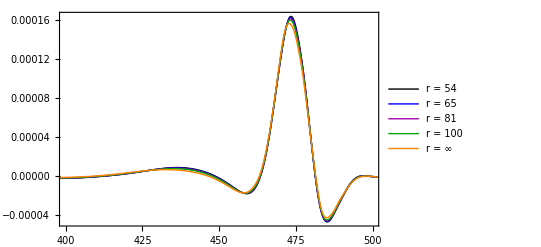

```mathematica
PresentationListLinePlot[Append[shiftedpDots,pDot],PlotRange->{{400,500},All},PlotLegend->labels]
```

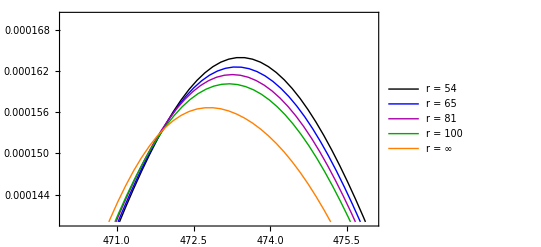

```mathematica
PresentationListLinePlot[Append[shiftedpDots,pDot],PlotRange->{{470,476},{0.00014,0.00017}},
PlotLegend->labels]
```